## Working with RawArrays

This example demonstrates working with RawArrays. It requires Mathematica 11.1 or later because it uses the BinarySerialize function.

RawArray support in LTemplate requires Mathematica 10.4 or later.

```mathematica
Needs["LTemplate`"]
SetDirectory@NotebookDirectory[];
```

```mathematica
template=
LClass["RA",
{
LFun["shuffle",{{LType[List,Real,1],"Constant"}},LType[RawArray,"UnsignedInteger8"]],
LFun["deshuffle",{{LType[RawArray,"UnsignedInteger8"],"Constant"}},LType[List,Real,1]]
}
];
```

```mathematica
CompileTemplate[template]
```

Current directory is: /Users/szhorvat/Repos/LTemplate/LTemplate/Documentation/Examples/RawArray

Unloading library RA ...

Generating library code ...

Compiling library code ...

/Users/szhorvat/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/RA.dylib

```mathematica
LoadTemplate[template]
```

```mathematica
obj=Make[RA];
```

This table of real numbers takes up 800 kB of storage.

```mathematica
data=Table[Sin[x],{x,0,100,0.001}];
```

```mathematica
ByteCount[data]
```

800152

However, there is a lot of redundancy in the numbers as they represent a continuous function.

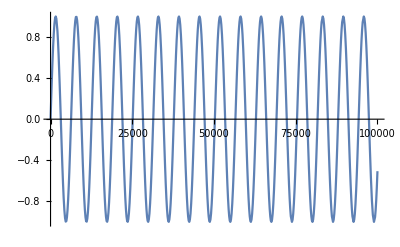

```mathematica
ListLinePlot[data,MaxPlotPoints->500]
```

It is reasonable to expect this data to compress well, but BinarySerialize does not do very well on it. The result is 750 kB, only a 6% reduction from the original size.

```mathematica
BinarySerialize[data,PerformanceGoal->"Size"]
```

ByteArray[…]

```mathematica
ByteCount[%]/ByteCount[data]//N
```

0.938001

The compressibility can be improved considerably by rearranging the underlying bytes of the data so that the first byte of each floating point number are stored contiguously, followed by the second bytes, and so on. This exposes the redundancy in the data. The shuffle function performs this rearranging.

```mathematica
obj@"shuffle"[data]
```

RawArray[UnsignedInteger8,<800008>]

```mathematica
BinarySerialize[obj@"shuffle"[data],PerformanceGoal->"Size"]
```

ByteArray[…]

Now we have a 31% reduction.

```mathematica
ByteCount[%]/ByteCount[data]//N
```

0.685031

The compressibility could be improved further (at the cost of some numerical accuracy) by storing only the differences between the consecutive numbers.  The following functions implement this:

```mathematica
compress[data_?(VectorQ[#,Developer`MachineRealQ]&)]:=
BinarySerialize[
obj@"shuffle"[Prepend[Differences[data],First[data]]],
PerformanceGoal->"Size"
]
```

```mathematica
decompress[bytes_]:=Accumulate[obj@"deshuffle"[BinaryDeserialize[bytes]]]
```

```mathematica
compress[data]
```

ByteArray[…]

This way we could achieve a 45% reduction in size.

```mathematica
ByteCount@compress[data]/ByteCount[data]//N
```

0.550042

For practical purposes, the accuracy loss is negligible.

```mathematica
Abs[decompress@compress[data]-data]//Max
```

4.33681×10^-19